```mathematica
DropMore[symbol_,n_]:=Block[{name=SymbolName[symbol],result,mult=1, current=Null,node,max},
result=name;
max=StringLength[StringDelete[name,"x"]]-1;
For[current=max,current> n, current--,
node=ToString[current];
If[StringEndsQ[result,"x"<>node],
mult*=(n-1);result=StringDrop[result,-2],
result=StringDelete[result,node]
];
If[StringEndsQ[result,"x"],
Interrupt[];
result=StringDrop[result,-1]
];
];
Simplify[mult*Symbol[result]]
]
```

```mathematica
MobiusGraph4[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[from[[1]],to[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

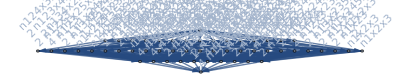

```mathematica
MobiusGraph4[k5Key,allGraphs5]
```

```mathematica
repFormatted=Table[allGraphs5[k,"colofourrealnull"]->Style[DropMore[allGraphs5[k,"colofourrealnull"],4],Red],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5→3 n1x2x3x4,n12x3x4x5→3 n12x3x4,n123x4x5→3 n123x4,n1234x5→3 n1234,n12345→n1234,n1235x4→n123x4,n123x45→n123x4,n124x3x5→3 n124x3,n1245x3→n124x3,n124x35→n124x3,n125x3x4→n12x3x4,n125x34→n12x34,n12x34x5→3 n12x34,n12x345→n12x34,n12x35x4→n12x3x4,n12x3x45→n12x3x4,n13x2x4x5→3 n13x2x4,n134x2x5→3 n134x2,n1345x2→n134x2,n134x25→n134x2,n135x2x4→n13x2x4,n135x24→n13x24,n13x24x5→3 n13x24,n13x245→n13x24,n13x25x4→n13x2x4,n13x2x45→n13x2x4,n14x2x3x5→3 n14x2x3,n145x2x3→n14x2x3,n145x23→n14x23,n14x23x5→3 n14x23,n14x235→n14x23,n14x25x3→n14x2x3,n14x2x35→n14x2x3,n15x2x3x4→n1x2x3x4,n15x23x4→n1x23x4,n15x234→n1x234,n15x24x3→n1x24x3,n15x2x34→n1x2x34,n1x23x4x5→3 n1x23x4,n1x234x5→3 n1x234,n1x2345→n1x234,n1x235x4→n1x23x4,n1x23x45→n1x23x4,n1x24x3x5→3 n1x24x3,n1x245x3→n1x24x3,n1x24x35→n1x24x3,n1x25x3x4→n1x2x3x4,n1x25x34→n1x2x34,n1x2x34x5→3 n1x2x34,n1x2x345→n1x2x34,n1x2x35x4→n1x2x3x4,n1x2x3x45→n1x2x3x4}

```mathematica
repUnFormatted=Table[allGraphs5[k,"colofourrealnull"]->DropMore[allGraphs5[k,"colofourrealnull"],4],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5→3 n1x2x3x4,n12x3x4x5→3 n12x3x4,n123x4x5→3 n123x4,n1234x5→3 n1234,n12345→n1234,n1235x4→n123x4,n123x45→n123x4,n124x3x5→3 n124x3,n1245x3→n124x3,n124x35→n124x3,n125x3x4→n12x3x4,n125x34→n12x34,n12x34x5→3 n12x34,n12x345→n12x34,n12x35x4→n12x3x4,n12x3x45→n12x3x4,n13x2x4x5→3 n13x2x4,n134x2x5→3 n134x2,n1345x2→n134x2,n134x25→n134x2,n135x2x4→n13x2x4,n135x24→n13x24,n13x24x5→3 n13x24,n13x245→n13x24,n13x25x4→n13x2x4,n13x2x45→n13x2x4,n14x2x3x5→3 n14x2x3,n145x2x3→n14x2x3,n145x23→n14x23,n14x23x5→3 n14x23,n14x235→n14x23,n14x25x3→n14x2x3,n14x2x35→n14x2x3,n15x2x3x4→n1x2x3x4,n15x23x4→n1x23x4,n15x234→n1x234,n15x24x3→n1x24x3,n15x2x34→n1x2x34,n1x23x4x5→3 n1x23x4,n1x234x5→3 n1x234,n1x2345→n1x234,n1x235x4→n1x23x4,n1x23x45→n1x23x4,n1x24x3x5→3 n1x24x3,n1x245x3→n1x24x3,n1x24x35→n1x24x3,n1x25x3x4→n1x2x3x4,n1x25x34→n1x2x34,n1x2x34x5→3 n1x2x34,n1x2x345→n1x2x34,n1x2x35x4→n1x2x3x4,n1x2x3x45→n1x2x3x4}

```mathematica
allGraphs5[k5Key,"colofourrealnull"]/.repFormatted//Sort
```

24 n1234-6 (3 n1234)-8 n123x4+2 (3 n123x4)-8 n124x3+2 (3 n124x3)-4 n12x34+3 n12x34+4 n12x3x4-3 n12x3x4-8 n134x2+2 (3 n134x2)-4 n13x24+3 n13x24+4 n13x2x4-3 n13x2x4-4 n14x23+3 n14x23+4 n14x2x3-3 n14x2x3-8 n1x234+2 (3 n1x234)+4 n1x23x4-3 n1x23x4+4 n1x24x3-3 n1x24x3+4 n1x2x34-3 n1x2x34-4 n1x2x3x4+3 n1x2x3x4

```mathematica
Simplify[(allGraphs5[k5Key,"colofourrealnull"]/.repUnFormatted)==-allGraphs[K4Key,"colofourrealnull"]]
```

True

```mathematica
allGraphs5[k5Key,"colofourrealnull"]
```

24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

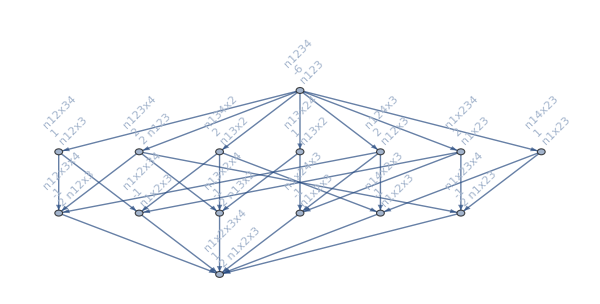

```mathematica
MobiusGraph4[K4Key,allGraphs]
```